```mathematica
(* We want to investigate why quadrature of f[y] converges exponentially quick. The literature indicates periodic functions (and function with all their derivatives equalling zero at boundaries (?)) have this property. *)
```

```mathematica
f[y_,x0_,x2_,n_,g_,K_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]If[y<g,1,0]
```

```mathematica
(* We see the derivative at the boundary is zero, regardless of x0 and x2. *)
```

```mathematica
Manipulate[Plot[f[y,x0,x2,n,g,1] ,{y,-3,g},PlotRange->{{-3,3},{0,1}}],{x0,-1,g-1/n},{x2,-1,g + 1/n},{g,0.5,2},{n,3,10}]
```

```mathematica
(* If we zoom to y = g, we see there is a smooth transition to 0*)
```

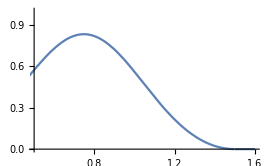

```mathematica
Plot[f[y,0.6,0.9,6,1.5,1] ,{y,-3,1.6},PlotRange->{{0.5,1.6},{0,1}}]
```

```mathematica
(* Removing the indicator function, since Fourier transforms of functions in bounded domains are annoying*)
```

```mathematica
f2[y_,x0_,x2_,n_,g_,K_]:=(1 - Exp[-2 n(g+K/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - K/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]
```

```mathematica
(* It appears that the function is symmetric around g. Fiddling around with x0 and x2 shows that they fade away at extreme values. Values of g just move them away from the center. Higher values of n force the peaks downwards.*)
```

```mathematica
Manipulate[Plot[Abs[f2[y+g,x0,x2,n,g,1] ],{y,-7,7},PlotRange->{{-7,7},{0,1}}],{x0,-5,g},{x2,-5,g},{g,0.5,2},{n,3,10}]
```

```mathematica
(* Defining f^g as the Fourier transform of the shifted f*)
```

```mathematica
fshift[y_]:=f2[y+g,x0,x2,n,g,K ]
```

```mathematica
Assuming[n>0 &&g>0 && Element[K, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[fshift[t],t,s,FourierParameters->{0,-2Pi}]]
```

(ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 K-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 K+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n)/(2 √π)

```mathematica
fshifthat[s_,n_]:=1/(2 √π)ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 K-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 K+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n
```

```mathematica
(*Using symmetry property of funcction (see 2019-03-17 research notes), we get the error term from the PSF*)
```

```mathematica
error[h_,n_]:=1/2 Re[∑_(k=-30)^30 fshifthat[k/h,n]-fshifthat[0,n]/. g-> 1/. x2-> 0/.x0-> 0/. K-> 1]
```

```mathematica
N[error[1/10,5],10]
```

2.349776437×10^-86

```mathematica
(* Defining the Riemann sum approximation of the integral*)
```

```mathematica
riemann[h_,x0_,x2_,n_,g_]:=h∑_(k =-8/h)^(1/h) f2[k h,x0,x2,n,g,1]
```

```mathematica
Abs[NIntegrate[f2[y,x0,x2,n,g,K]/. g-> 1/. n -> 5 /. x2-> 0/.x0-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100] -N[ riemann[1/10,0,0,5,1],100]]
```

2.3497764374359×10^-86

```mathematica
(*Plotting the error in approximating with a Riemann sum. It seems pretty robust against x0 and x2 also.*)
```

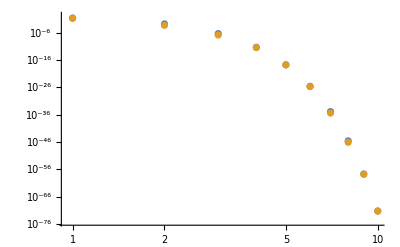

```mathematica
ListLogLogPlot[{Table[Abs[NIntegrate[f2[y,x0,x2,n,g,K]/. g-> 1/. n -> 6 /.x0-> 0/. x2-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100] - N[riemann[1/M,0,0,6,1],100]],{M,1,10}],
Table[Abs[NIntegrate[f2[y,x0,x2,n,g,K]/. g-> 1/. n -> 6 /.x0-> 0/. x2-> 1/5/. K-> 1,{y,-∞,1},WorkingPrecision->100] - N[riemann[1/M,0,1/5,6,1],100]],{M,1,10}]}]
```

```mathematica
Table[error[1/M,5]/. g-> 1 /. x2-> 0/.x0-> 0/. K-> 1//N,{M,1,10}]
```

{0.175273,0.000472868,2.44583×10^-8,2.41878×10^-14,4.63178×10^-22,1.73116×10^-31,1.25287×10^-42,1.73366×10^-55,4.58676×10^-70,2.34978×10^-86}

```mathematica
Table[Abs[NIntegrate[f2[y,x0,x2,n,g,K]/. g-> 1/. n -> 5 /. x2-> 0/.x0-> 0/. K-> 1,{y,-∞,1},WorkingPrecision->100] - N[riemann[1/M,0,0,5,1],100]],{M,1,10}]
```

{0.175272819007981275521438465134661178007158842092931012708839071734277266806803900293887788605837912,0.000472868335384879437888974270999821683490736145438560200995097724379808639120957913060750202752147,2.4458256959747814631572236511681013276341382372504268912819566038615952368232320867764248674×10^-8,2.4187838215622138789790412070652398733750829444056777117502846847546841440499142978462×10^-14,4.63177542327365848492622870203682588480250025043613494215087662451101167518924×10^-22,1.73116369303858067923777946335518975659675563499950462232328663586339×10^-31,1.252874770224340034445311686931449266941377023274461967847×10^-42,1.73365818298240962800916406795084674888792085×10^-55,4.58675523807705924741415238556×10^-70,2.3497764374359×10^-86}

```mathematica
(*After some manipulation of the Fourier transform of f^g, we get the following expression.*)
```

```mathematica
summanderror[s_,x0_,x2_,n_,g_,K_]:=√(n/π)Exp[-n/2(2 g^2+x0^2+x2^2-2g(x0 +x2))](Exp[1/(4n)(2 n g - n(x0 +x2) +2 π s)(2 n g - n (x0 +x2)-2π s)]Cos[2 π s (2 n g - n(x0 +x2))/(4 n)]-
Exp[1/(4n)(2 K + n(x0 -x2) +2 π s)(2 K + n(x0 -x2)-2π s)]Cos[2 π s (2 K + n(x0 -x2))/(4 n)])
```

```mathematica
(*Something wrong with the signs... magnitude looks ok though*)
```

```mathematica
N[fshifthat[10,16],10]/. x0 ->0 /.x2-> 0/. g-> 1 /. K-> 1
```

3.664528×10^-27+0. ⅈ

```mathematica
N[summanderror[10,0,0,16,1,1],10]
```

3.664527732×10^-27

```mathematica
Plot3D[summanderror[4,x0,x2,3,1,1],{x0,-3,1},{x2,-3,1},PlotRange->Full,PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->8]
```

-Graphics3D-

```mathematica
(* Just comparing with the case when i = n*)
```

```mathematica
f3[y_,x2_,n_,g_]:=(1 - Exp[-2 n(g-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]If[y<g,1,0]
```

```mathematica
(* As y approaches the boundary, the derivatives of the function explode. This is made even more extreme as we send x2 towards g also.*)
```

```mathematica
Manipulate[Plot[f3[y,x2,n,g] ,{y,-3,g},PlotRange->{{-3,3},{0,1}}],{x2,-1,g},{g,0.5,2},{n,3,10}]
```

```mathematica
(* As we send y x2 to g, *)
```

```mathematica
Evaluate[D[f3[y,x2,n,g],y]]/.y-> g
```

-ⅇ^(-1/2 n (-g+x2)^2) n^(3/2) √(2/π) (g-x2) If[g<g,1,0]

```mathematica
(*  We see the function becomes negative, so any type of Riemann sum will give 0 identically. This doesn't allow us to to use the PSF trick*)
```

```mathematica
Manipulate[Plot[(1 - Exp[-2 n(g-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y] ,{y,-6,6},PlotRange->{{-6,6},{-1,1}}],{x2,-1,g},{g,0.5,2},{n,3,10}]
```

```mathematica
riemann2[h_,g_,n_]:=h∑_(k =-8/h)^(1/h) f3[k h,0,n,g]
```

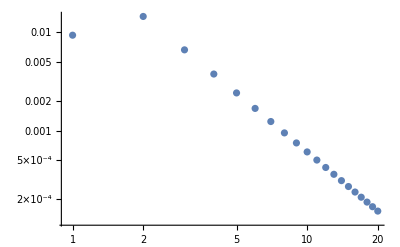

```mathematica
ListLogLogPlot[{Table[Abs[NIntegrate[f3[y,0,5,1],{y,-∞,1},WorkingPrecision->100] -N[riemann2[1/M,1,5],100]],{M,1,20}]}]
```